```mathematica
(*   
      **********************
          DEFINITIONS
    **********************
*)
```

```mathematica
coords = {t, x, θ, φ};
```

```mathematica
ps = ψ[t, x];
be = β[t, x];
al = α[t, x];
phi = Φ[t, x];
pi = Π[t, x];
phi2 = ξ[t, x];
pi2 = Ξ[t, x];
ghost = ϕ[t, x];
r2 = x^2 + l^2;
areal = r[x];
id4 = IdentityMatrix[4];
```

```mathematica
psj = Subscript[ψ, j];
bej = Subscript[β, j];
alj = Subscript[α, j];
psjp1 = Subscript[ψ, j+1];
bejp1 = Subscript[β, j+1];
aljp1 = Subscript[α, j+1];
psjm1 = Subscript[ψ, j-1];
bejm1 = Subscript[β, j-1];
aljm1 = Subscript[α, j-1];
```

```mathematica
phiDef = D[ghost, x];
piDef = ((ps^2)/al)*(D[ghost, t] - be*D[ghost, x]);
rsq = areal^2;
```

```mathematica
r2ps4 = r2 * (ps^4);
rsqPs4 = rsq*(ps^4);
dtphiDef = D[phiDef, t];
dtpiDef = D[piDef, t];
dxphi = D[phiDef, x];
dxpi = D[piDef, x];
dtal = D[al, t];
dtbe = D[be, t];
dtps = D[ps, t];
dxal = D[al, x];
dxbe = D[be, x];
dxps = D[ps, x];
dtphi = D[phi,t];
dtpi =  D[pi,t];
dxphi = D[phi,x];
dxpi =  D[pi,x];
dtphi2 = D[phi2,t];
dtpi2 =  D[pi2,t];
dxphi2 = D[phi2,x];
dxpi2 =  D[pi2,x];
```

```mathematica
dx2al = D[dxal,x];
dx2be = D[dxbe,x];
dx2ps = D[dxps,x];
dxdtal = D[dxal,t];
dxdtbe = D[dxbe,t];
dxdtps = D[dxps,t];
dt2ps = D[dtps,t];
```

```mathematica
ghostSol = ArcTan[x/l]/ (2*Sqrt[Pi]);
alSol = 1;
beSol = 0;
psSol = 1;
xiSol = l/(2*Sqrt[Pi]*r2);
piSol = 0;
xi2Sol = 0;
pi2Sol = 0;
```

```mathematica
infal = 1 + a1/Sqrt[r2] + a2/r2;
infbe = b1/Sqrt[r2] + b2/r2;
infps = 1 + c1/Sqrt[r2] + c2/r2;
```

```mathematica
rinfal = 1 + a1/areal + a2/rsq;
rinfbe = b1/areal + b2/rsq;
rinfps = 1 + c1/areal + c2/rsq;
```

```mathematica
fieldDerivatives = {dxphi, dxpi, dtphi, dtpi, dxphi2, dxpi2, dtphi2, dtpi2, dxal, dxbe, dxps, dtal, dtbe, dtps, dxdtal, dxdtbe, dxdtps, dx2al, dx2be, dx2ps, dt2ps};
```

```mathematica
(*   
      **********************
          METRIC
    **********************
*)
```

```mathematica
metric = {{-(al^2) + (ps^4 )*(be^2), be*(ps^4), 0, 0},
{be*(ps^4), ps^4, 0, 0},
{0, 0, r2ps4, 0},
{0, 0, 0, r2ps4*(Sin[θ]^2)}}
```

{{-α[t,x]^2+β[t,x]^2 ψ[t,x]^4,β[t,x] ψ[t,x]^4,0,0},{β[t,x] ψ[t,x]^4,ψ[t,x]^4,0,0},{0,0,(l^2+x^2) ψ[t,x]^4,0},{0,0,0,(l^2+x^2) Sin[θ]^2 ψ[t,x]^4}}

```mathematica
rMetric = {{-(al^2) + (ps^4 )*(be^2), be*(ps^4), 0, 0},
{be*(ps^4), ps^4, 0, 0},
{0, 0, rsqPs4, 0},
{0, 0, 0, rsqPs4*(Sin[θ]^2)}};
```

```mathematica
metricInv = Simplify[Inverse[metric]]
```

{{-1/α[t,x]^2,β[t,x]/α[t,x]^2,0,0},{β[t,x]/α[t,x]^2,-β[t,x]^2/α[t,x]^2+1/ψ[t,x]^4,0,0},{0,0,1/((l^2+x^2) ψ[t,x]^4),0},{0,0,0,Csc[θ]^2/((l^2+x^2) ψ[t,x]^4)}}

```mathematica
rMetricInv = Simplify[Inverse[rMetric]];
```

```mathematica
metDet = Simplify[Det[metric]]
```

-(l^2+x^2)^2 Sin[θ]^2 α[t,x]^2 ψ[t,x]^12

```mathematica
rMetDet = Simplify[Det[rMetric]];
```

```mathematica
(*   
      **********************
     SPATIAL SLICING
    **********************
*)
```

```mathematica
nL = {-al, 0, 0, 0}
```

{-α[t,x],0,0,0}

```mathematica
nU = metricInv.nL
```

{1/α[t,x],-β[t,x]/α[t,x],0,0}

```mathematica
spatialMetric = metric + Outer[Times, nL, nL]
spatialMetricInv = metricInv + Outer[Times, nU, nU];
spatialProjUL = id4 + Outer[Times, nU, nL];
spatialProjLU = id4 + Outer[Times, nL, nU];
rSpatialMetric = rMetric + Outer[Times, nL, nL];
rSpatialMetricInv = rMetricInv + Outer[Times, nU, nU]
```

{{β[t,x]^2 ψ[t,x]^4,β[t,x] ψ[t,x]^4,0,0},{β[t,x] ψ[t,x]^4,ψ[t,x]^4,0,0},{0,0,(l^2+x^2) ψ[t,x]^4,0},{0,0,0,(l^2+x^2) Sin[θ]^2 ψ[t,x]^4}}

{{0,0,0,0},{0,1/ψ[t,x]^4,0,0},{0,0,1/(r[x]^2 ψ[t,x]^4),0},{0,0,0,Csc[θ]^2/(r[x]^2 ψ[t,x]^4)}}

```mathematica
spatialMetDet = Simplify[Det[Table[spatialMetric[[a,b]],{a,2,4},{b,2,4}]]]
```

(l^2+x^2)^2 Sin[θ]^2 ψ[t,x]^12

```mathematica
rSpatialMetDet = Simplify[Det[Table[rSpatialMetric[[a,b]],{a,2,4},{b,2,4}]]];
```

```mathematica
(*   
   **********************************************************
                   FUNCTIONS 
   **********************************************************
*)
```

```mathematica
christoffelULL[g_, ginv_] := Simplify[Table[(1/2)*Sum[ginv[[u1,dd]]*(D[g[[dd,l1]], coords[[l2]]] + D[g[[dd, l2]], coords[[l1]]] - D[g[[l1, l2]], coords[[dd]]]),{dd,1, 4}], {u1, 1, 4}, {l1, 1, 4}, {l2, 1, 4}]];

riemannULLL[connectULL_] :=  Simplify[Table[D[connectULL[[u1,l1,l3]], coords[[l2]]] - D[connectULL[[u1,l1,l2]], coords[[l3]]] + Sum[connectULL[[dd,l1,l3]]*connectULL[[u1,dd,l2]],{dd,1, 4}] - Sum[connectULL[[ee,l1,l2]]*connectULL[[u1,ee,l3]],{ee,1, 4}], {u1, 1, 4}, {l1, 1, 4}, {l2, 1, 4}, {l3, 1, 4}]];

ricciLL[riemULLL_] := Simplify[Table[Sum[riemULLL[[dd, l1, dd, l2]],{dd,1, 4}], {l1, 1, 4}, {l2, 1, 4}]];

ricciScalar[ricLL_, ginv_] := Simplify[Sum[ginv[[dd,ee]]*ricLL[[ee,dd]],{dd, 1, 4}, {ee, 1, 4}]];

dU[vec_, connectULL_] := Simplify[Table[D[vec[[vecInd]], coords[[dInd]]] + Sum[vec[[dd]]*connectULL[[vecInd, dInd, dd]], {dd, 1, 4}], {dInd,1,4},{vecInd,1,4}]];

dL[form_, connectULL_] := Simplify[Table[D[form[[formInd]], coords[[dInd]]] - Sum[form[[dd]]*connectULL[[dd, dInd, formInd]], {dd, 1, 4}], {dInd,1,4},{formInd,1,4}]];

dUU[tUU_, connectULL_] := Simplify[Table[D[tUU[[u1, u2]], coords[[dInd]]] + Sum[connectULL[[u1, dInd, dd]]*tUU[[dd, u2]], {dd, 1, 4}] + Sum[connectULL[[u2, dInd, ee]]*tUU[[u1, ee]], {ee, 1, 4}], {dInd,1,4},{u1,1,4},{u2,1,4}]];

dLL[tLL_,connectULL_] := Simplify[Table[D[tLL[[l1, l2]], coords[[dInd]]] - Sum[connectULL[[dd, dInd, l1]]*tLL[[dd, l2]], {dd, 1, 4}] - Sum[connectULL[[ee, dInd, l2]]*tLL[[l1, ee]], {ee, 1, 4}],{dInd,1,4},{l1,1,4},{l2,1,4}]];
```

```mathematica
dLspatial[form_, connectULL_, projLU_] := Block[{dlFull},
dlFull = dL[form, connectULL];
Simplify[Table[Sum[projLU[[dInd, dd]]*dlFull[[dd]], {dd, 1, 4}], {dInd,1,4}]]];

dUspatial[vec_, connectULL_, projLU_] := Block[{duFull},
duFull = dU[vec, connectULL];
Simplify[Table[Sum[projLU[[dInd, dd]]*duFull[[dd]], {dd, 1, 4}], {dInd,1,4}]]];

dLLspatial[form_, connectULL_, projLU_] := Block[{dllFull},
dllFull = dLL[form, connectULL];
Simplify[Table[Sum[projLU[[dInd1,dd]]*projLU[[dInd2,ee]]*dllFull[[dd,ee]], {dd, 1, 4}, {ee,1,4}], {dInd1,1,4}, {dInd2,1,4}]]];

dUUspatial[form_, connectULL_, projLU_] := Block[{duuFull},
duuFull = dUU[form, connectULL];
Simplify[Table[Sum[projLU[[dInd1,dd]]*projLU[[dInd2,ee]]*duuFull[[dd,ee]], {dd, 1, 4}, {ee,1,4}], {dInd1,1,4}, {dInd2,1,4}]]];

scalarDspatial[scalar_, projLU_] := Simplify[Table[Sum[projLU[[dInd, dd]]*D[scalar, coords[[dd]]], {dd, 1, 4}], {dInd,1,4}]];
```

```mathematica
d2scalar[scalar_,  connectULL_] := dL[Table[D[scalar, coords[[aa]]],{aa,1,4}], connectULL];

d2scalarSpatial[scalar_,  connectULL_, projLU_] := dLspatial[scalarDspatial[scalar,projLU], connectULL, projLU];
```

```mathematica
Clean[expr_]:=HoldForm[expr]/.(h:Except[HoldForm|Equal|Power|Times|Plus|Log|Subscript | Rational | Complex|List|Derivative|Rule|SeriesData])[args___]:>h
```

```mathematica
(*   
   **********************************************************
                  GEOMETRIC OBJECTS
   **********************************************************
*)
```

```mathematica
connection4ULL = christoffelULL[metric, metricInv];
connection3ULL = christoffelULL[spatialMetric, spatialMetricInv];
rConnection4ULL = christoffelULL[rMetric, rMetricInv];
rConnection3ULL = christoffelULL[rSpatialMetric, rSpatialMetricInv];
```

```mathematica
riemann4ULLL = riemannULLL[connection4ULL];
riemann3ULLL = riemannULLL[connection3ULL];
rRiemann4ULLL = riemannULLL[rConnection4ULL];
rRiemann3ULLL = riemannULLL[rConnection3ULL];
```

```mathematica
ricci4LL = ricciLL[riemann4ULLL];
ricci3LL = ricciLL[riemann3ULLL];
rRicci4LL = ricciLL[rRiemann4ULLL];
rRicci3LL = ricciLL[rRiemann3ULLL];
```

```mathematica
ricciScalar4 = ricciScalar[ricci4LL, metricInv];
ricciScalar3 = ricciScalar[ricci3LL, spatialMetricInv];
rRicciScalar4 = ricciScalar[rRicci4LL, rMetricInv];
rRicciScalar3 = ricciScalar[rRicci3LL, rSpatialMetricInv];
```

```mathematica
(*   CHECK METRIC COMPATIBILITY   *)
```

```mathematica
dLnL = dL[nL, connection4ULL];
```

```mathematica
dLnU = dU[nU, connection4ULL];
```

```mathematica
dLnUlow = Simplify[Table[Sum[metric[[dd,bc]]*dLnU[[ac,dd]],{dd,1,4}],{ac,1,4},{bc,1,4}]];
dLnLup = Simplify[Table[Sum[metricInv[[dd,bc]]*dLnL[[ac,dd]],{dd,1,4}],{ac,1,4},{bc,1,4}]];
```

```mathematica
Simplify[dLnL - dLnUlow]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Simplify[dLnU - dLnLup]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Simplify[Table[Sum[nU[[dd]]*spatialMetric[[dd,ac]],{dd,1,4}],{ac,1,4}]]
```

{0,0,0,0}

```mathematica
rdLnL = dL[nL, rConnection4ULL];
```

```mathematica
rdLnU = dU[nU, rConnection4ULL];
```

```mathematica
dLL3spatialMetric = dLL[spatialMetric,connection3ULL];
```

```mathematica
dLL4spatialMetric = dLL[spatialMetric,connection4ULL];
```

```mathematica
dLLspatial3 = Simplify[Table[Sum[spatialProjLU[[aa,dd]]*spatialProjLU[[bb,ee]]*spatialProjLU[[cc,ff]]*dLL3spatialMetric[[dd,ee,ff]],{dd,1,4},{ee,1,4},{ff,1,4}],{aa,1,4},{bb,1,4},{cc,1,4}]]
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
dLLspatial4 = Simplify[Table[Sum[spatialProjLU[[aa,dd]]*spatialProjLU[[bb,ee]]*spatialProjLU[[cc,ff]]*dLL4spatialMetric[[dd,ee,ff]],{dd,1,4},{ee,1,4},{ff,1,4}],{aa,1,4},{bb,1,4},{cc,1,4}]]
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
(*   CHECK LIE DERIVATIVE   *)
```

```mathematica
symdLnL = Simplify[Table[dLnL[[ac,bc]] + dLnL[[bc,ac]],{ac,1,4},{bc,1,4}]];
lieDmetric = Simplify[Table[ Sum[nU[[c1]]*D[metric[[a,b]], coords[[c1]]], {c1,1,4}] + Sum[metric[[a, c2]]*D[nU[[c2]], coords[[b]]],{c2,1, 4}] + Sum[metric[[c3, b]]*D[nU[[c3]], coords[[a]]],{c3,1, 4}], {a,1,4}, {b,1,4}]];
Simplify[lieDmetric - symdLnL]
{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(*   
      **********************
     EXTRINSIC CURVATURE
    **********************
*)
```

```mathematica
kext = Simplify[Table[ -(1/2)*(Sum[nU[[c1]]*D[spatialMetric[[a,b]], coords[[c1]]], {c1,1,4}] + Sum[spatialMetric[[a, c2]]*D[nU[[c2]], coords[[b]]],{c2,1, 4}] + Sum[spatialMetric[[c3, b]]*D[nU[[c3]], coords[[a]]],{c3,1, 4}]), {a,1,4}, {b,1,4}]];
```

```mathematica
kextmean = Simplify[Sum[spatialMetricInv[[aa,bb]] * kext[[bb,aa]],{bb,1, 4},{aa,1, 4}]];
```

```mathematica
maxSliceDtPs = be*D[ps,x] + (ps/6)*(D[be,x] + (2*x*be/(l^2 + x^2)));
```

```mathematica
kextUL = Simplify[Table[Sum[spatialMetricInv[[uu,bb]] * kext[[bb,ll]],{bb,1, 4}],{ll,1,4},{uu,1, 4}]];
kextUU = Simplify[Table[Sum[spatialMetricInv[[u2,cc]]*spatialMetricInv[[u1,bb]] * kext[[bb,cc]],{bb,1, 4},{cc,1,4}],{u1,1,4},{u2,1, 4}]];
Simplify[kextUU - Simplify[Table[Sum[metricInv[[u2,cc]]*metricInv[[u1,bb]] * kext[[bb,cc]],{bb,1, 4},{cc,1,4}],{u1,1,4},{u2,1, 4}]]]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
dUU4kext = dUU[kextUU, connection4ULL];
dUU3kext = dUU[kextUU, connection3ULL];
```

```mathematica
dSpatialUU3kext = Simplify[Table[Sum[spatialProjLU[[aa,dd]]*spatialProjLU[[ee,bb]]*spatialProjLU[[ff,cc]]*dUU3kext[[dd,ee,ff]],{dd,1,4},{ee,1,4},{ff,1,4}],{aa,1,4},{bb,1,4},{cc,1,4}]];
dSpatialUU4kext = Simplify[Table[Sum[spatialProjLU[[aa,dd]]*spatialProjLU[[ee,bb]]*spatialProjLU[[ff,cc]]*dUU4kext[[dd,ee,ff]],{dd,1,4},{ee,1,4},{ff,1,4}],{aa,1,4},{bb,1,4},{cc,1,4}]];
```

```mathematica
Simplify[dSpatialUU3kext - dSpatialUU4kext]
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
dSpatial3kmean = Simplify[Table[Sum[spatialMetric[[aa,bb]]*dSpatialUU3kext[[ll,aa,bb]],{aa,1,4},{bb,1,4}],{ll,1,4}]];
dSpatial4kmean = Simplify[Table[Sum[spatialMetric[[aa,bb]]*dSpatialUU4kext[[ll,aa,bb]],{aa,1,4},{bb,1,4}],{ll,1,4}]];
Simplify[dSpatial3kmean - dSpatial4kmean]
```

{0,0,0,0}

```mathematica
dSpatialKmean = Simplify[Table[Sum[spatialProjLU[[ll,bb]]*D[kextmean,coords[[bb]]],{bb,1,4}],{ll,1,4}]];
```

```mathematica
Simplify[dSpatial4kmean - dSpatialKmean]
```

{0,0,0,0}

```mathematica
kUUmean = Simplify[Sum[kextUU[[aa,bb]]*spatialMetric[[aa,bb]],{aa,1,4},{bb,1,4}]];
Simplify[kextmean - kUUmean];
```

```mathematica
div3kUU = Simplify[Table[Sum[dSpatialUU3kext[[dd,dd,uu]],{dd,2,4}],{uu,1,4}]];
div4kUU = Simplify[Table[Sum[dSpatialUU3kext[[dd,dd,uu]],{dd,1,4}],{uu,1,4}]];
Simplify[div3kUU - div4kUU]
```

{0,0,0,0}

```mathematica
dUspatialKmean = Simplify[Table[Sum[spatialMetricInv[[uu,ll]]*dSpatialKmean[[ll]],{ll,1,4}],{uu,1,4}]];
Simplify[dSpatial3kmean - dSpatialKmean];
```

```mathematica
kext2 = Simplify[Table[-Sum[spatialProjLU[[l1,dd]]*spatialProjLU[[l2,ee]]*dLnL[[dd,ee]],{dd,1,4},{ee,1,4}],{l1,1,4},{l2,1,4}]];
kext2mean = Simplify[Sum[spatialMetricInv[[dd,ee]] * kext2[[ee,dd]],{dd,1, 4},{ee,1, 4}]];
```

```mathematica
accel = Simplify[Table[Sum[nU[[cc]]*dLnL[[cc, a]],{cc,1,4}], {a,1,4}]];
Simplify[accel - Table[Sum[spatialProjLU[[ac,dd]]*D[Log[al],coords[[dd]]],{dd,1,4}],{ac,1,4}]];
Simplify[Sum[nU[[dd]]*accel[[dd]],{dd,1,4}]];
kext3 = Simplify[-(dLnL + Outer[Times, nL, accel])];
Simplify[kext - kext3]; Simplify[kext - kext2];
```

```mathematica
rKext = Simplify[Table[-Sum[spatialProjLU[[l1,dd]]*spatialProjLU[[l2,ee]]*rdLnL[[dd,ee]],{dd,1,4},{ee,1,4}],{l1,1,4},{l2,1,4}]];
```

```mathematica
rKextmean = Simplify[Sum[rSpatialMetricInv[[a,b]] * rKext[[b,a]],{b,1, 4},{a,1, 4}]]
```

(2 β[t,x] (ψ[t,x] r'[x]+3 r[x] ψ^(0,1)[t,x])+r[x] (ψ[t,x] β^(0,1)[t,x]-6 ψ^(1,0)[t,x]))/(r[x] α[t,x] ψ[t,x])

```mathematica
Simplify[(al*ps/6)*rKextmean]
```

(β[t,x] ψ[t,x] r'[x])/(3 r[x])+1/6 ψ[t,x] β^(0,1)[t,x]+β[t,x] ψ^(0,1)[t,x]-ψ^(1,0)[t,x]

```mathematica
rKext2 = Simplify[Table[ -(1/2)*(Sum[nU[[c1]]*D[rSpatialMetric[[a,b]], coords[[c1]]], {c1,1,4}] + Sum[rSpatialMetric[[a, c2]]*D[nU[[c2]], coords[[b]]],{c2,1, 4}] + Sum[rSpatialMetric[[c3, b]]*D[nU[[c3]], coords[[a]]],{c3,1, 4}]), {a,1,4}, {b,1,4}]];
```

```mathematica
Simplify[rKext - rKext2]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Simplify[rKextmean - Sum[rMetricInv[[a,b]] * rKext[[b,a]],{b,1, 4},{a,1, 4}]]
```

0

```mathematica
rMaxSliceDtPs = be*D[ps,x] + (ps/6)*(D[be,x] + (be*D[rsq,x]/rsq));
```

```mathematica
rKextUU = Simplify[Table[Sum[rSpatialMetricInv[[u2,cc]]*rSpatialMetricInv[[u1,bb]] * rKext[[bb,cc]],{bb,1, 4},{cc,1,4}],{u1,1,4},{u2,1, 4}]];
```

```mathematica
(*   FLAT TEST   *)
```

```mathematica
metricFlat = {{-1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}};
metricFlatInv = Inverse[metricFlat];
```

```mathematica
flatConnect = christoffelULL[metricFlat, metricFlatInv];
flatRicci = riemannULLL[flatConnect];
```

```mathematica
ricciScalarFlat = ricciScalar[flatRicci, metricFlatInv]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(*   MASS ASPECT   *)
```

```mathematica
maspectDef = Simplify[0.5*Sqrt[r2ps4]*(1 - Sum[metricInv[[cc,dd]]*D[Sqrt[r2ps4], coords[[cc]]]*D[Sqrt[r2ps4], coords[[dd]]],{cc,1,4},{dd,1,4}])];
```

```mathematica
maspectHand = Simplify[(Sqrt[r2ps4]/2)*(1 - (D[Sqrt[r2ps4],x]/(ps^2))^2 + (r2ps4/(9*(al^2)))*((dxbe - x*be/r2)^2))]
```

1/2 √((l^2+x^2) ψ[t,x]^4) (1+((l^2+x^2) ψ[t,x]^4 (-(x β[t,x])/(l^2+x^2)+β^(0,1)[t,x])^2)/(9 α[t,x]^2)-((x ψ[t,x]+2 (l^2+x^2) ψ^(0,1)[t,x])^2)/((l^2+x^2) ψ[t,x]^2))

```mathematica
Simplify[maspectHand /. {dtps->maxSliceDtPs, ps->1, al->1, be->0, dxbe->0, dxps->0} ]
```

l^2/(2 √(l^2+x^2))

```mathematica
Simplify[maspectDef - (Sqrt[r2ps4]/2)*(1 + r2*(((ps^2)*(dxbe - x*be/r2)/(3*al))^2 - (x/r2 + 2*dxps/ps)^2)) /. dtps->maxSliceDtPs];
```

```mathematica
normSinfU = {0,1/(ps^2),0,0};
normSinfL = metric.normSinfU;
```

```mathematica
metricSinf = spatialMetric - Outer[Times,normSinfL,normSinfL]
```

{{0,0,0,0},{0,0,0,0},{0,0,(l^2+x^2) ψ[t,x]^4,0},{0,0,0,(l^2+x^2) Sin[θ]^2 ψ[t,x]^4}}

```mathematica
detSinf = Simplify[Det[Table[metricSinf[[ii,jj]],{ii,3,4},{jj,3,4}]]]
```

(l^2+x^2)^2 Sin[θ]^2 ψ[t,x]^8

```mathematica
madmIntegrand = Simplify[r2ps4*Sin[coords[[3]]]*Sum[normSinfL[[ii]]*(spatialMetricInv[[nn,mm]]*connection3ULL[[ii,nn,mm]] - spatialMetricInv[[ii,mm]]*connection3ULL[[nn,mm,nn]]),{ii,2,4},{nn,2,4},{mm,2,4}]];
```

```mathematica
(*   NULL EXPANSION   *)
```

```mathematica
nullVec = nU + {0, 1/(ps^2), 0, 0};
revnullVec = nU - {0, 1/(ps^2), 0, 0};
```

```mathematica
outnullDef = Simplify[(2/Sqrt[r2ps4])*Sum[nullVec[[cc]]*D[Sqrt[r2ps4], coords[[cc]]],{cc,1,4}]];
revnullDef = Simplify[(2/Sqrt[r2ps4])*Sum[revnullVec[[cc]]*D[Sqrt[r2ps4], coords[[cc]]],{cc,1,4}]];
```

```mathematica
outnullHand = Simplify[2*((x/r2 + 2*dxps/ps)/(ps^2) + (dxbe - x*be/r2)/(3*al))];
revnullHand = Simplify[2*((dxbe - x*be/r2)/(3*al) - (2*dxps/ps + x/r2)/(ps^2))]
```

(2 (-(x β[t,x])/(l^2+x^2)+β^(0,1)[t,x]))/(3 α[t,x])+(2 (-(x ψ[t,x])/(l^2+x^2)-2 ψ^(0,1)[t,x]))/ψ[t,x]^3

```mathematica
Simplify[outnullDef - outnullHand /. dtps->maxSliceDtPs]
```

0

```mathematica
Simplify[revnullDef - revnullHand /. dtps->maxSliceDtPs]
```

0

```mathematica
(*   
     **********************************************************
   **********************************************************
                    EQUATIONS OF MOTION   
   **********************************************************
   **********************************************************
*)
```

```mathematica
eomTable = Table[D[ghost,coords[[ac]],coords[[bc]]] - Sum[connection4ULL[[cc,ac,bc]]*D[ghost,coords[[cc]]],{cc,1, 4}],{ac,1 ,4},{bc, 1,4}];
```

```mathematica
eomGhost = Simplify[Sum[metricInv[[b, a]]*eomTable[[a,b]], {a, 1, 4}, {b, 1, 4}]];
```

```mathematica
setGhost = Simplify[Table[-D[ghost,coords[[m]]]*D[ghost,coords[[n]]] + (1/2)*metric[[m,n]]*Sum[metricInv[[a,b]]*D[ghost,coords[[a]]]*D[ghost,coords[[b]]],{a,1, 4},{b,1, 4}], {m,1,4}, {n,1,4}]];
```

```mathematica
setGhostUU = Simplify[Table[Sum[metricInv[[u1,cc]]*metricInv[[u2,dd]]*setGhost[[cc,dd]],{cc,1,4},{dd,1,4}],{u1,1,4},{u2,1,4}]];
```

```mathematica
Simplify[eomGhost*(al*(ps^2)) + dtpi - (1/(r2*(ps^4)))*D[(r2*(ps^4))*(be*piDef + (al/(ps^2))*phiDef),x] + 4*dtps*piDef/ps];
```

```mathematica
eomCompact = Simplify[(D[r2ps4*(be*piDef + (al/(ps^2))*phiDef),x] - D[r2ps4*piDef,t]) / r2ps4];
```

```mathematica
Simplify[setGhost[[1,1]] + (1/2)*((al*piDef/(ps^2) +  be*phiDef)^2 + (be*piDef + al*phiDef/(ps^2))^2)]
```

0

```mathematica
Simplify[setGhost[[1,2]] + (1/2)*be*(phiDef^2 + piDef^2) +  al*phiDef*piDef/(ps^2)]
```

0

```mathematica
Simplify[setGhost[[2,2]] + (1/2)*(phiDef^2 + piDef^2)]
```

0

```mathematica
Simplify[setGhost[[3,3]] - (r2/2)*(phiDef^2 - piDef^2)]
```

0

```mathematica
Simplify[(Sin[coords[[3]]]^2)*setGhost[[3,3]] - setGhost[[4,4]]]
```

0

```mathematica
Ttt = (-1/2)*((al*pi/(ps^2) + be*phi)^2 + (al*phi/(ps^2) + be*pi)^2);
```

```mathematica
Ttx = (-1/2)*(be*(pi^2 + phi^2) + (2*al/(ps^2))*phi*pi);
```

```mathematica
Txx = (-1/2)*(pi^2 + phi^2);
```

```mathematica
Thh = (r2/2)*(phi^2 - pi^2);
```

```mathematica
setTotal = (1/2)* {{((al*pi2/(ps^2) +  be*phi2)^2 + (be*pi2 + al*phi2/(ps^2))^2 - (al*pi/(ps^2) +  be*phi)^2 - (be*pi + al*phi/(ps^2))^2), be*(phi2^2 + pi2^2 - phi^2 - pi^2) +  2*al*(phi2*pi2 - pi*phi)/(ps^2), 0, 0}, {be*(phi2^2 + pi2^2 - phi^2 - pi^2) +  2*al*(phi2*pi2 - pi*phi)/(ps^2), phi2^2 + pi2^2 - phi^2 - pi^2, 0, 0}, {0, 0, r2*(phi^2 - pi^2 - phi2^2 + pi2^2), 0}, {0, 0, 0, r2*(Sin[coords[[3]]]^2)*(phi^2 - pi^2 - phi2^2 + pi2^2)}};
```

```mathematica
setTotalUU = Simplify[Table[Sum[metricInv[[u1,cc]]*metricInv[[u2,dd]]*setTotal[[cc,dd]],{cc,1,4},{dd,1,4}],{u1,1,4},{u2,1,4}]];
```

```mathematica
setTrace = Simplify[Sum[metricInv[[aa,bb]]*setTotal[[aa,bb]], {aa,1,4}, {bb,1,4}]]
```

(-ξ[t,x]^2+Ξ[t,x]^2-Π[t,x]^2+Φ[t,x]^2)/ψ[t,x]^4

```mathematica
setGhostTrace = Simplify[Sum[metricInv[[aa,bb]]*setGhost[[aa,bb]], {aa,1,4}, {bb,1,4}]] ;
```

```mathematica
Simplify[setGhostTrace - Simplify[setTrace /. {phi2->0, pi2->0, phi->phiDef, pi->piDef}]]
```

0

```mathematica
Simplify[setGhost - Simplify[setTotal /. {phi2->0, pi2->0, phi->phiDef, pi->piDef}]]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(*   Hamiltonian Constraint   *)
```

```mathematica
energyDensity = Sum[nU[[ac]]*nU[[bc]]*setGhost[[ac,bc]], {ac,1,4}, {bc,1,4}];
```

```mathematica
totalEnergyDensity =  Simplify[Sum[nU[[aa]]*nU[[bb]]*setTotal[[aa,bb]], {aa,1,4}, {bb,1,4}]]
```

(ξ[t,x]^2+Ξ[t,x]^2-Π[t,x]^2-Φ[t,x]^2)/(2 ψ[t,x]^4)

```mathematica
Simplify[(-1/(2*(ps^4)))*(piDef^2 + phiDef^2) - energyDensity]
```

0

```mathematica
hamiltonianLHS = Simplify[ricciScalar3 + kextmean^2 - Sum[Sum[metricInv[[cc,d1]]*metricInv[[bb,d2]]*kext[[d1,d2]]*kext[[cc,bb]],{d1,1,4},{d2,1,4}],{cc,1,4},{bb,1,4}]];
```

```mathematica
hamSub = Simplify[hamiltonianLHS /. D[ps,t]-> maxSliceDtPs];
```

```mathematica
hamSlice = Simplify[(-ps^5/8)*hamSub];
```

```mathematica
hamiltonianConstraint = Simplify[(-ps^5/8)*hamSub - Pi*ps*(pi^2 + phi^2)];
```

```mathematica
rHamiltonianLHS = Simplify[rRicciScalar3 + rKextmean^2 - Sum[Sum[rMetricInv[[ac,d1]]*rMetricInv[[bc,d2]]*rKext[[d1,d2]]*rKext[[ac,bc]],{d1,1,4},{d2,1,4}],{ac,1,4},{bc,1,4}]];
```

```mathematica
rHamSub = Simplify[rHamiltonianLHS /. D[ps,t]-> rMaxSliceDtPs];
```

```mathematica
rHamSlice = Simplify[(-ps^5/8)*rHamSub];
```

```mathematica
Clean[rHamSlice /. {D[areal,x] -> 1, D[D[areal,x],x] -> 0}]
```

(ψ^5 (β-r β^(0,1))^2+12 r α^2 (2 ψ^(0,1)+r ψ^(0,2)))/(12 r^2 α^2)

```mathematica
resHam = Simplify[hamiltonianLHS  -  16*Pi*totalEnergyDensity];
```

```mathematica
(*   Momentum Constraint   *)
```

```mathematica
momentumDensity = Simplify[Table[-Sum[spatialProjUL[[bc,ac]]*nU[[cc]]*setGhost[[bc,cc]],{bc,1,4},{cc,1,4}],{ac,1,4}]]
```

{(β[t,x] ϕ^(0,1)[t,x] (-β[t,x] ϕ^(0,1)[t,x]+ϕ^(1,0)[t,x]))/α[t,x],(ϕ^(0,1)[t,x] (-β[t,x] ϕ^(0,1)[t,x]+ϕ^(1,0)[t,x]))/α[t,x],0,0}

```mathematica
totalMomentumL = Simplify[Table[-Sum[spatialProjLU[[ac,bc]]*nU[[cc]]*setTotal[[bc,cc]],{bc,1,4},{cc,1,4}],{ac,1,4}]];
```

```mathematica
totalMomentumU = Simplify[Table[-Sum[spatialMetricInv[[ac,bc]]*nU[[cc]]*setTotal[[bc,cc]],{bc,1,4},{cc,1,4}],{ac,1,4}]];
```

```mathematica
Simplify[totalMomentumU - spatialMetricInv.totalMomentumL]
```

{0,0,0,0}

```mathematica
Simplify[totalMomentumL - Table[-Sum[spatialProjLU[[ac,bc]]*nU[[cc]]*setTotal[[bc,cc]],{bc,2,4},{cc,1,4}],{ac,1,4}]]
```

{0,0,0,0}

```mathematica
momLHSl = Simplify[Table[Sum[spatialMetric[[ii,jj]]*div4kUU[[jj]],{jj,2,4}],{ii,1,4}] - dSpatialKmean];
```

```mathematica
momLHSu = Simplify[div4kUU - dUspatialKmean];
```

```mathematica
Simplify[momLHSl - (spatialMetric.div4kUU - dSpatialKmean)]
```

{0,0,0,0}

```mathematica
Simplify[momLHSu - (div4kUU - spatialMetricInv.Table[D[kext2mean, coords[[aa]]], {aa,1,4}])]
```

{0,0,0,0}

```mathematica
Simplify[spatialMetricInv.momentumDensity]
```

{0,(ϕ^(0,1)[t,x] (-β[t,x] ϕ^(0,1)[t,x]+ϕ^(1,0)[t,x]))/(α[t,x] ψ[t,x]^4),0,0}

```mathematica
xUmomentum = phi*pi/(ps^6);
xLmomentum = phi*pi/(ps^2);
xLtotalMomentum = (phi*pi - phi2*pi2)/(ps^2);
```

```mathematica
Simplify[momLHSl[[2]] - momLHSu[[2]]*(ps^4)]
```

0

```mathematica
momLHSuSub = Simplify[momLHSu /. {D[ps,t]-> maxSliceDtPs, D[D[ps,t],x]->D[maxSliceDtPs,x]}];
```

```mathematica
momentumConstraint = Simplify[(3*al*(ps^4)/2)*(momLHSuSub[[2]] - 8*Pi*xUmomentum)];
```

```mathematica
resMomLvec = Simplify[momLHSl - 8*Pi*totalMomentumL];
```

```mathematica
resMomUvec = Simplify[momLHSu - 8*Pi*totalMomentumU];
```

```mathematica
resMom = resMomLvec[[2]];
```

```mathematica
(*   Slicing Constraint   *)
```

```mathematica
setTotalSpatial = Simplify[Table[Sum[spatialMetric[[ii,cc]]*spatialMetric[[jj,dd]]*setTotalUU[[cc,dd]],{cc,1,4},{dd,1,4}],{ii,1,4},{jj,1,4}]];
```

```mathematica
setTotalSpatialTrace = Simplify[Sum[spatialMetricInv[[ii,jj]]*setTotalSpatial[[ii,jj]],{ii,2,4},{jj,2,4}]]
```

(-ξ[t,x]^2+3 Ξ[t,x]^2-3 Π[t,x]^2+Φ[t,x]^2)/(2 ψ[t,x]^4)

```mathematica
Simplify[setTotalSpatialTrace - Sum[spatialMetricInv[[ii,jj]]*setTotalSpatial[[ii,jj]],{ii,1,4},{jj,1,4}]]
```

0

```mathematica
(* OLD *)
```

```mathematica
spatialMetricIJonly = Simplify[Table[spatialMetric[[a,b]],{a,2,4},{b,2,4}]];spatialMetricInvIJonly = Simplify[Table[spatialMetricInv[[a,b]],{a,2,4},{b,2,4}]];
```

```mathematica
setSpatial = Simplify[Table[Sum[spatialProjLU[[ii,cc]]*spatialProjLU[[jj,dd]]*setGhost[[cc,dd]],{cc,1,4},{dd,1,4}],{ii,1,4},{jj,1,4}]];
Simplify[setSpatial - Table[Sum[spatialMetric[[aa,ll1]]*spatialMetric[[bb,ll2]]*setGhostUU[[aa,bb]],{aa,1,4},{bb,1,4}],{ll1,1,4},{ll2,1,4}]]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
setSpatialIJ = Simplify[Table[Sum[spatialMetric[[ii,cc]]*spatialMetric[[jj,dd]]*setGhostUU[[cc,dd]],{cc,1,4},{dd,1,4}],{ii,2,4},{jj,2,4}]];
```

```mathematica
Simplify[Table[setSpatial[[ii,jj]],{ii,2,4},{jj,2,4}] - setSpatialIJ]
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
setSpatialIJspatialSum = Simplify[Table[Sum[spatialMetric[[ii,cc]]*spatialMetric[[jj,dd]]*setGhostUU[[cc,dd]],{cc,2,4},{dd,2,4}],{ii,2,4},{jj,2,4}]];
```

```mathematica
Simplify[setSpatialIJ - setSpatialIJspatialSum]
```

{{1/(2 α[t,x]^4)β[t,x] ψ[t,x]^4 (β[t,x] ψ[t,x]^4 (-β[t,x] ϕ^(0,1)[t,x]+ϕ^(1,0)[t,x])^2+α[t,x]^2 ϕ^(0,1)[t,x] (-3 β[t,x] ϕ^(0,1)[t,x]+4 ϕ^(1,0)[t,x])),0,0},{0,0,0},{0,0,0}}

```mathematica
setSpatialTrace = Simplify[Sum[spatialMetricInvIJonly[[ii,jj]]*setSpatialIJ[[ii,jj]],{ii,1,3},{jj,1,3}]]
```

(α[t,x]^2 (ϕ^(0,1)[t,x])^2-3 ψ[t,x]^4 (-β[t,x] ϕ^(0,1)[t,x]+ϕ^(1,0)[t,x])^2)/(2 α[t,x]^2 ψ[t,x]^4)

```mathematica
energyDensitySpatial = (-1/(2*(ps^4)))*(phi^2 + pi^2 );
```

```mathematica
setScalarSpatial = (1/(2*(ps^4)))*(phi^2 - 3*(pi^2 ));
```

```mathematica
Simplify[energyDensitySpatial + setScalarSpatial]
```

-(2 Π[t,x]^2)/ψ[t,x]^4

```mathematica
boxAlSpatial = Simplify[Sum[D[Sqrt[spatialMetDet]*spatialMetricInv[[ii,jj]]*D[al,coords[[jj]]], coords[[ii]]],{ii,1,4},{jj,1,4}]/Sqrt[spatialMetDet]];
```

```mathematica
boxAlSpatialLL = d2scalarSpatial[al, connection4ULL, spatialProjLU];
```

```mathematica
rBoxAlSpatial = Simplify[Sum[D[Sqrt[rSpatialMetDet]*rSpatialMetricInv[[ii,jj]]*D[al,coords[[jj]]], coords[[ii]]],{ii,1,4},{jj,1,4}]/Sqrt[rSpatialMetDet]];
```

```mathematica
Simplify[boxAlSpatial - Sum[D[Sqrt[spatialMetDet]*spatialMetricInv[[ii,jj]]*D[al,coords[[jj]]], coords[[ii]]],{ii,2,4},{jj,2,4}]/Sqrt[spatialMetDet]]
```

0

```mathematica
Simplify[boxAlSpatial - Sum[spatialMetricInv[[aa,bb]]*boxAlSpatialLL[[aa,bb]],{aa,1,4}, {bb,1,4}]]
```

0

```mathematica
dtkextTotal = Simplify[-boxAlSpatial + al*(Sum[kext[[ii,jj]]*kextUU[[ii,jj]],{ii,2,4},{jj,2,4}] + 4*Pi*(totalEnergyDensity + setTotalSpatialTrace)) + be*Part[scalarDspatial[kextmean,spatialProjLU],2]];
```

```mathematica
Simplify[dtkextTotal - Simplify[-boxAlSpatial + al*(Sum[kext[[ii,jj]]*kextUU[[ii,jj]],{ii,1,4},{jj,1,4}] + 4*Pi*(totalEnergyDensity + setTotalSpatialTrace)) + be*D[kextmean,x]]]
```

0

```mathematica
dtKextmean = Simplify[-boxAlSpatial + al*(Sum[kext[[ii,jj]]*kextUU[[ii,jj]],{ii,2,4},{jj,2,4}] + 4*Pi*(energyDensitySpatial + setScalarSpatial)) + be*D[kextmean,x]];
```

```mathematica
Simplify[dtKextmean - (-boxAlSpatial + al*(Sum[kext[[ii,jj]]*kextUU[[ii,jj]],{ii,1,4},{jj,1,4}] + 4*Pi*(energyDensitySpatial + setScalarSpatial)) + be*Sum[spatialProjLU[[2,aa]]*D[kextmean,coords[[aa]]],{aa,1,4}])];
```

```mathematica
(* TEST DTK *)
```

```mathematica
testDTK = Simplify[-rBoxAlSpatial + al*(Sum[rKext[[ii,jj]]*rKextUU[[ii,jj]],{ii,2,4},{jj,2,4}] + 4*Pi*(energyDensitySpatial + setScalarSpatial)) + be*D[rKextmean,x]];
```

```mathematica
testDTKsub = Simplify[testDTK /. {dtps->rMaxSliceDtPs, D[dtps,x]->D[rMaxSliceDtPs,x]}];
```

```mathematica
testDTKekg = Simplify[testDTKsub /. {D[areal,x]->1,D[D[areal,x],x]->0, areal->x}]
```

-(8 π α[t,x] Π[t,x]^2)/ψ[t,x]^4+(2 (β[t,x]-x β^(0,1)[t,x])^2)/(3 x^2 α[t,x])-(2 x α^(0,1)[t,x] ψ^(0,1)[t,x]+ψ[t,x] (2 α^(0,1)[t,x]+x α^(0,2)[t,x]))/(x ψ[t,x]^5)

```mathematica
Simplify[testDTKekg*(-ps^4)]
```

8 π α[t,x] Π[t,x]^2-(2 ψ[t,x]^4 (β[t,x]-x β^(0,1)[t,x])^2)/(3 x^2 α[t,x])+2 α^(0,1)[t,x] (1/x+(ψ^(0,1)[t,x])/ψ[t,x])+α^(0,2)[t,x]

```mathematica
Clean[%]
```

8 π α Π^2-(2 ψ^4 (β-x β^(0,1))^2)/(3 x^2 α)+2 α^(0,1) (1/x+ψ^(0,1)/ψ)+α^(0,2)

```mathematica
testDTKwh = Simplify[testDTKsub /. {D[areal,x]-> D[Sqrt[r2],x],D[D[areal,x],x]->D[D[Sqrt[r2],x],x], areal->Sqrt[r2]}];
```

```mathematica
Clean[%]
```

-(8 π α Π^2)/ψ^4-(2 x α^(0,1))/((l^2+x^2) ψ^4)+(2 (x β-(l^2+x^2) β^(0,1))^2)/(3 (l^2+x^2)^2 α)-(2 α^(0,1) ψ^(0,1))/ψ^5-α^(0,2)/ψ^4

```mathematica
dtKextmeanSub = Simplify[dtKextmean /. {dtps->maxSliceDtPs, D[dtps,x]->D[maxSliceDtPs,x]}]
```

-(8 π α[t,x] Π[t,x]^2)/ψ[t,x]^4-(2 x α^(0,1)[t,x])/((l^2+x^2) ψ[t,x]^4)+(2 (x β[t,x]-(l^2+x^2) β^(0,1)[t,x])^2)/(3 (l^2+x^2)^2 α[t,x])-(2 α^(0,1)[t,x] ψ^(0,1)[t,x])/ψ[t,x]^5-(α^(0,2)[t,x])/ψ[t,x]^4

```mathematica
Clean[dtKextmeanSub]
```

-(8 π α Π^2)/ψ^4-(2 x α^(0,1))/((l^2+x^2) ψ^4)+(2 (x β-(l^2+x^2) β^(0,1))^2)/(3 (l^2+x^2)^2 α)-(2 α^(0,1) ψ^(0,1))/ψ^5-α^(0,2)/ψ^4

```mathematica
Simplify[testDTKwh - dtKextmeanSub]
```

0

```mathematica
(*
     EOM & BOUNDARY CONDITION CHECKING
*)
```

```mathematica
oldalEOM = D[dxal,x] + 2*dxal*((x/r2) + (dxps/ps)) - (2*(ps^4)/(3*al))*((x/r2)*be - dxbe)^2 + 8*Pi*al*(pi^2);
Simplify[oldalEOM  + dtKextmeanSub*(ps^4)];
```

```mathematica
alEOM = dx2al + 2*dxal*((x/r2) + (dxps/ps)) - (2*(ps^4)/(3*al))*((x/r2)*be - dxbe)^2 + 8*Pi*al*(pi^2 - pi2^2);
Simplify[alEOM  + Simplify[dtkextTotal*(ps^4) /. {dtps->maxSliceDtPs, D[dtps,x]->D[maxSliceDtPs,x]}]]
```

0

```mathematica
oldbetaEOM = D[D[be,x],x] - ((x/r2)*be - D[be,x])*((2*x/r2) + (6*dxps/ps) - (dxal/al)) - ((l/r2)^2)*be - (12*Pi*al*phi*pi/(ps^2));
Simplify[oldbetaEOM - momentumConstraint];
```

```mathematica
betaEOM = dx2be - ((x/r2)*be - dxbe)*((2*x/r2) + (6*dxps/ps) - (dxal/al)) - ((l/r2)^2)*be - (12*Pi*al*(phi*pi - phi2*pi2)/(ps^2));Simplify[betaEOM - Simplify[(3*al*(ps^4)/2)*resMomUvec[[2]] /. {dtps->maxSliceDtPs, D[dtps,x]->D[maxSliceDtPs,x]}]]
```

0

```mathematica
oldpsiEOM = dx2ps +(2*x/r2)*dxps + ((ps^5)/(12*(al^2)))*((x/r2)*be - dxbe)^2 + ((l^2*ps)/(4*(r2^2))) - Pi*(phi^2 + pi^2 - phi2^2 - pi2^2)*ps;
Simplify[oldpsiEOM - hamiltonianConstraint];
```

```mathematica
psiEOM = dx2ps +(2*x/r2)*dxps + ((ps^5)/(12*(al^2)))*((x/r2)*be - dxbe)^2 + ((l^2*ps)/(4*(r2^2))) - Pi*(phi^2 + pi^2 - phi2^2 - pi2^2)*ps;Simplify[psiEOM - Simplify[(-ps^5/8)*resHam /. {dtps->maxSliceDtPs, D[dtps,x]->D[maxSliceDtPs,x]}]]
```

0

```mathematica
piEOM = Simplify[(D[r2ps4*pi,t] - D[r2ps4*(be*pi + (al/(ps^2))*phi),x]) / r2ps4];
phiEOM = Simplify[dtphi - D[(al/(ps^2))*pi + be*phi,x]];
psiHYP = Simplify[dtps -be*dxps - (ps/6)*(dxbe + (2*x/r2)*be)];
pi2EOM = Simplify[(D[r2ps4*pi2,t] - D[r2ps4*(be*pi2 + (al/(ps^2))*phi2),x]) / r2ps4];
phi2EOM = Simplify[dtphi2 - D[(al/(ps^2))*pi2 + be*phi2,x]];
```

```mathematica
alEOMr = D[dxal,x] + 2*dxal*((x/rsq) + (dxps/ps)) - (2*(ps^4)/(3*al))*((x/rsq)*be - dxbe)^2 + 8*Pi*al*(pi^2);
```

```mathematica
betaEOMr = D[D[be,x],x] - ((x/rsq)*be - D[be,x])*((2*x/rsq) + (6*D[ps,x]/ps) - (D[al,x]/al)) - ((l/rsq)^2)*be - (12*Pi*al*phi*pi/(ps^2));
```

```mathematica
psiEOMr = D[D[ps,x],x] +(2*x/rsq)*D[ps,x] + ((ps^5)/(12*(al^2)))*((x/rsq)*be - D[be,x])^2 + ((l^2*ps)/(4*(rsq^2))) - Pi*(phi^2 + pi^2)*ps;
```

```mathematica
(* BOUNDARY CONDITIONS *)
rinfalEOM = Simplify[Simplify[Simplify[alEOMr/.{al->rinfal, dxal->D[rinfal,x], dx2al->D[D[rinfal,x],x], be->rinfbe, dxbe->D[rinfbe,x], dx2be->D[D[rinfbe,x],x], ps->rinfps, dxps->D[rinfps,x], dx2ps->D[D[rinfps,x],x], pi->0, phi->(l/(2*Sqrt[Pi]))*(1/rsq)}]/.{D[areal,x]->x/areal, D[D[areal,x],x]->(1 - (x^2)/rsq)/areal}] /. x^2 -> rsq-l^2];
rinfbetaEOM = Simplify[Simplify[Simplify[betaEOMr/.{al->rinfal, dxal->D[rinfal,x], dx2al->D[D[rinfal,x],x], be->rinfbe, dxbe->D[rinfbe,x], dx2be->D[D[rinfbe,x],x], ps->rinfps, dxps->D[rinfps,x], dx2ps->D[D[rinfps,x],x], pi->0, phi->(l/(2*Sqrt[Pi]))*(1/rsq)}]/.{D[areal,x]->x/areal, D[D[areal,x],x]->(1 - (x^2)/rsq)/areal}] /. x^2 -> rsq-l^2];
rinfpsiEOM = Simplify[Simplify[Simplify[psiEOMr/.{al->rinfal, dxal->D[rinfal,x], dx2al->D[D[rinfal,x],x], be->rinfbe, dxbe->D[rinfbe,x], dx2be->D[D[rinfbe,x],x], ps->rinfps, dxps->D[rinfps,x], dx2ps->D[D[rinfps,x],x], pi->0, phi->(l/(2*Sqrt[Pi]))*(1/rsq)}]/.{D[areal,x]->x/areal, D[D[areal,x],x]->(1 - (x^2)/rsq)/areal}] /. x^2 -> rsq-l^2];
```

```mathematica
Series[rinfalEOM,{areal, Infinity, 5}]
```

(2 (a2+a1 c1))/r[x]^4+(4 a2 c1-2 a1 c1^2+4 a1 c2-a1 l^2)/r[x]^5+O[1/r[x]]^6

```mathematica
Series[rinfbetaEOM,{areal, Infinity, 5}]
```

-(2 b1)/r[x]^3+(-2 a1 b1+12 b1 c1)/r[x]^4+(2 a1^2 b1-4 a2 b1-3 a1 b2+18 b2 c1-12 b1 c1^2+24 b1 c2)/r[x]^5+O[1/r[x]]^6

```mathematica
Series[rinfpsiEOM,{areal, Infinity, 5}]
```

(2 c2)/r[x]^4-(c1 l^2)/r[x]^5+O[1/r[x]]^6

```mathematica
infalEOM = Simplify[alEOM/.{al->infal, dxal->D[infal,x], dx2al->D[D[infal,x],x], be->infbe, dxbe->D[infbe,x], dx2be->D[D[infbe,x],x], ps->infps, dxps->D[infps,x], dx2ps->D[D[infps,x],x], pi->0, phi->(l/(2*Sqrt[Pi]))*(1/r2)}];
infbetaEOM = Simplify[betaEOM/.{al->infal, dxal->D[infal,x], dx2al->D[D[infal,x],x], be->infbe, dxbe->D[infbe,x], dx2be->D[D[infbe,x],x], ps->infps, dxps->D[infps,x], dx2ps->D[D[infps,x],x], pi->0, phi->(l/(2*Sqrt[Pi]))*(1/r2)}];
infpsiEOM = Simplify[psiEOM/.{al->infal, dxal->D[infal,x], dx2al->D[D[infal,x],x], be->infbe, dxbe->D[infbe,x], dx2be->D[D[infbe,x],x], ps->infps, dxps->D[infps,x], dx2ps->D[D[infps,x],x], pi->0, phi->(l/(2*Sqrt[Pi]))*(1/r2)}];
```

```mathematica
rXseries = Series[Sqrt[r2], {x, Infinity, 4}]
```

x+l^2/(2 x)-l^4/(8 x^3)+O[1/x]^5

```mathematica
rXmseries = Series[Sqrt[r2], {x, -Infinity, 4}]
```

-x-l^2/(2 x)+l^4/(8 x^3)+O[1/x]^5

```mathematica
x$rXseries = Series[x/Sqrt[r2], {x, Infinity, 4}]
```

1-l^2/(2 x^2)+(3 l^4)/(8 x^4)+O[1/x]^5

```mathematica
r$xXseries = Series[Sqrt[r2]/x, {x, Infinity, 4}]
```

1+l^2/(2 x^2)-l^4/(8 x^4)+O[1/x]^5

```mathematica
r2$xXseries = Series[r2/x, {x, Infinity, 4}]
```

x+l^2/x+O[1/x]^5

```mathematica
r2$x2Xseries = Series[r2/(x^2), {x, Infinity, 4}]
```

1+l^2/x^2+O[1/x]^5

```mathematica
infdxxps = ps + x*dxps
```

ψ[t,x]+x ψ^(0,1)[t,x]

```mathematica
infdxrps = x$rXseries*ps + rXseries*dxps
```

(1-l^2/(2 x^2)+(3 l^4)/(8 x^4)+O[1/x]^5) ψ[t,x]+(x+l^2/(2 x)-l^4/(8 x^3)+O[1/x]^5) ψ^(0,1)[t,x]

```mathematica
infdrxps = r$xXseries*ps + rXseries*dxps
```

(1+l^2/(2 x^2)-l^4/(8 x^4)+O[1/x]^5) ψ[t,x]+(x+l^2/(2 x)-l^4/(8 x^3)+O[1/x]^5) ψ^(0,1)[t,x]

```mathematica
infdrrps = ps + r2$xXseries*dxps
```

ψ[t,x]+(x+l^2/x+O[1/x]^5) ψ^(0,1)[t,x]

```mathematica
Series[Simplify[piDef /. {al->rinfal, be->rinfbe, ps->rinfps}], {areal, Infinity,4} ]
```

ϕ^(1,0)[t,x]+(-b1 ϕ^(0,1)[t,x]+(-a1+2 c1) ϕ^(1,0)[t,x])/r[x]+(-b2 ϕ^(0,1)[t,x]-b1 (-a1+2 c1) ϕ^(0,1)[t,x]+(a1^2-a2-2 a1 c1+c1^2+2 c2) ϕ^(1,0)[t,x])/r[x]^2+1/r[x]^3(-b2 (-a1+2 c1) ϕ^(0,1)[t,x]-b1 (a1^2-a2-2 a1 c1+c1^2+2 c2) ϕ^(0,1)[t,x]+(-a1^3+2 a1 a2+2 (a1^2-a2) c1+2 c1 c2-a1 (c1^2+2 c2)) ϕ^(1,0)[t,x])+1/r[x]^4(-b2 (a1^2-a2-2 a1 c1+c1^2+2 c2) ϕ^(0,1)[t,x]-b1 (-a1^3+2 a1 a2+2 (a1^2-a2) c1+2 c1 c2-a1 (c1^2+2 c2)) ϕ^(0,1)[t,x]+(a1^4-3 a1^2 a2+a2^2+2 (-a1^3+2 a1 a2) c1-2 a1 c1 c2+c2^2+(a1^2-a2) (c1^2+2 c2)) ϕ^(1,0)[t,x])+O[1/r[x]]^5

```mathematica
(*
   **************************
          JACOBIAN
  ************************** 
*)
```

```mathematica
alEOMgrid = Simplify[alEOM /. {al->alj, dxal->(aljp1-aljm1)/(2*Δx),D[dxal,x]->(aljp1 - 2*alj + aljm1)/(Δx^2)}];
```

```mathematica
jacaa = Simplify[D[alEOMgrid,alj]]
```

-2/Δx^2+8 π (-Ξ[t,x]^2+Π[t,x]^2)+(2 ψ[t,x]^4 (-(x β[t,x])/(l^2+x^2)+β^(0,1)[t,x])^2)/(3 α_j^2)

```mathematica
jacaap1 = Simplify[D[alEOMgrid,aljp1]]
```

(1+(x Δx)/(l^2+x^2)+(Δx ψ^(0,1)[t,x])/ψ[t,x])/Δx^2

```mathematica
jacaam1 = Simplify[D[alEOMgrid,aljm1]]
```

(1-Δx (x/(l^2+x^2)+(ψ^(0,1)[t,x])/ψ[t,x]))/Δx^2

```mathematica
beEOMgrid = Simplify[betaEOM /. {be->bej, dxbe->(bejp1-bejm1)/(2*Δx),D[dxbe,x]->(bejp1 - 2*bej + bejm1)/(Δx^2)}];
```

```mathematica
jacbb = Simplify[D[beEOMgrid,bej]]
```

-l^2/((l^2+x^2)^2)-2/Δx^2-(x ((2 x)/(l^2+x^2)-(α^(0,1)[t,x])/α[t,x]+(6 ψ^(0,1)[t,x])/ψ[t,x]))/(l^2+x^2)

```mathematica
Simplify[-l^2/((l^2+x^2)^2)-2/Δx^2-(x ((2 x)/(l^2+x^2)-(Derivative[0,1][α][t,x])/α[t,x]+(6 Derivative[0,1][ψ][t,x])/ψ[t,x]))/(l^2+x^2) - (-1/(l^2+x^2)-2/Δx^2-(x (x/(l^2+x^2)-(Derivative[0,1][α][t,x])/α[t,x]+(6 Derivative[0,1][ψ][t,x])/ψ[t,x]))/(l^2+x^2))]
```

0

```mathematica
jacbbp1 = Simplify[D[beEOMgrid,bejp1]]
```

(2+(2 x Δx)/(l^2+x^2)-(Δx α^(0,1)[t,x])/α[t,x]+(6 Δx ψ^(0,1)[t,x])/ψ[t,x])/(2 Δx^2)

```mathematica
jacbbm1 = Simplify[D[beEOMgrid,bejm1]]
```

1/Δx^2-((2 x)/(l^2+x^2)-(α^(0,1)[t,x])/α[t,x]+(6 ψ^(0,1)[t,x])/ψ[t,x])/(2 Δx)

```mathematica
psEOMgrid = Simplify[psiEOM /. {ps->psj, dxps->(psjp1-psjm1)/(2*Δx),D[dxps,x]->(psjp1 - 2*psj + psjm1)/(Δx^2)}];
```

```mathematica
jacpp = Simplify[D[psEOMgrid,psj]]
```

l^2/(4 (l^2+x^2)^2)-2/Δx^2+π (ξ[t,x]^2+Ξ[t,x]^2-Π[t,x]^2-Φ[t,x]^2)+(5 ψ_j^4 (-(x β[t,x])/(l^2+x^2)+β^(0,1)[t,x])^2)/(12 α[t,x]^2)

```mathematica
jacppp1 = Simplify[D[psEOMgrid,psjp1]]
```

(1+(x Δx)/(l^2+x^2))/Δx^2

```mathematica
jacppm1 = Simplify[D[psEOMgrid,psjm1]]
```

(1-(x Δx)/(l^2+x^2))/Δx^2

```mathematica
(* OFF DIAGONAL JACOBIAN *)
```

```mathematica
{ps->psj, dxps->(psjp1-psjm1)/(2*Δx)}
{be->bej, dxbe->(bejp1-bejm1)/(2*Δx)}
{al->alj, dxal->(aljp1-aljm1)/(2*Δx)}
```

{ψ[t,x]→ψ_j,ψ^(0,1)[t,x]→(-ψ_(-1+j)+ψ_(1+j))/(2 Δx)}

{β[t,x]→β_j,β^(0,1)[t,x]→(-β_(-1+j)+β_(1+j))/(2 Δx)}

{α[t,x]→α_j,α^(0,1)[t,x]→(-α_(-1+j)+α_(1+j))/(2 Δx)}

```mathematica
jacapGrid = Simplify[alEOM /. {ps->psj, dxps->(psjp1-psjm1)/(2*Δx)}];
jacabGrid = Simplify[alEOM /. {be->bej, dxbe->(bejp1-bejm1)/(2*Δx)}];
jacbpGrid = Simplify[betaEOM /. {ps->psj, dxps->(psjp1-psjm1)/(2*Δx)}];
jacbaGrid = Simplify[betaEOM /. {al->alj, dxal->(aljp1-aljm1)/(2*Δx)}];
jacpaGrid = Simplify[psiEOM /. {al->alj, dxal->(aljp1-aljm1)/(2*Δx)}];
jacpbGrid = Simplify[psiEOM /. {be->bej, dxbe->(bejp1-bejm1)/(2*Δx)}];
```

```mathematica
(* ALPHA OFF DIAGONAL *)
```

```mathematica
jac$ap = D[jacapGrid, psj]
```

-((-ψ_(-1+j)+ψ_(1+j)) α^(0,1)[t,x])/(Δx ψ_j^2)-(8 ψ_j^3 (-(x β[t,x])/(l^2+x^2)+β^(0,1)[t,x])^2)/(3 α[t,x])

```mathematica
jac$app1 = D[jacapGrid, psjp1]
```

(α^(0,1)[t,x])/(Δx ψ_j)

```mathematica
jac$apm1 = D[jacapGrid, psjm1]
```

-(α^(0,1)[t,x])/(Δx ψ_j)

```mathematica
jac$ab = D[jacabGrid, bej]
```

-(4 x ((x β_j)/(l^2+x^2)+(β_(-1+j)-β_(1+j))/(2 Δx)) ψ[t,x]^4)/(3 (l^2+x^2) α[t,x])

```mathematica
jac$abp1 = D[jacabGrid, bejp1]
```

(2 ((x β_j)/(l^2+x^2)+(β_(-1+j)-β_(1+j))/(2 Δx)) ψ[t,x]^4)/(3 Δx α[t,x])

```mathematica
jac$abm1 = D[jacabGrid, bejm1]
```

-(2 ((x β_j)/(l^2+x^2)+(β_(-1+j)-β_(1+j))/(2 Δx)) ψ[t,x]^4)/(3 Δx α[t,x])

```mathematica
(* BETA OFF DIAGONAL *)
```

```mathematica
jac$ba = D[jacbaGrid, alj]
```

(12 π (ξ[t,x] Ξ[t,x]-Π[t,x] Φ[t,x]))/ψ[t,x]^2+((α_(-1+j)-α_(1+j)) ((x β[t,x])/(l^2+x^2)-β^(0,1)[t,x]))/(2 Δx α_j^2)

```mathematica
jac$bap1 = D[jacbaGrid, aljp1]
```

((x β[t,x])/(l^2+x^2)-β^(0,1)[t,x])/(2 Δx α_j)

```mathematica
jac$bam1 = D[jacbaGrid, aljm1]
```

-((x β[t,x])/(l^2+x^2)-β^(0,1)[t,x])/(2 Δx α_j)

```mathematica
jac$bp = D[jacbpGrid, psj]
```

-(24 π α[t,x] (ξ[t,x] Ξ[t,x]-Π[t,x] Φ[t,x]))/ψ_j^3+(3 (-ψ_(-1+j)+ψ_(1+j)) ((x β[t,x])/(l^2+x^2)-β^(0,1)[t,x]))/(Δx ψ_j^2)

```mathematica
jac$bpp1 = D[jacbpGrid, psjp1]
```

-(3 ((x β[t,x])/(l^2+x^2)-β^(0,1)[t,x]))/(Δx ψ_j)

```mathematica
jac$bpm1 = D[jacbpGrid, psjm1]
```

(3 ((x β[t,x])/(l^2+x^2)-β^(0,1)[t,x]))/(Δx ψ_j)

```mathematica
(* PSI OFF DIAGONAL *)
```

```mathematica
jac$pa = D[jacpaGrid, alj]
```

-(ψ[t,x]^5 (-(x β[t,x])/(l^2+x^2)+β^(0,1)[t,x])^2)/(6 α_j^3)

```mathematica
jac$pap1 = D[jacpaGrid, aljp1]
```

0

```mathematica
jac$pam1 = D[jacpaGrid, aljm1]
```

0

```mathematica
jac$pb = D[jacpbGrid, bej]
```

(x ((x β_j)/(l^2+x^2)+(β_(-1+j)-β_(1+j))/(2 Δx)) ψ[t,x]^5)/(6 (l^2+x^2) α[t,x]^2)

```mathematica
jac$pbp1 = D[jacpbGrid, bejp1]
```

-(((x β_j)/(l^2+x^2)+(β_(-1+j)-β_(1+j))/(2 Δx)) ψ[t,x]^5)/(12 Δx α[t,x]^2)

```mathematica
jac$pbm1 = D[jacpbGrid, bejm1]
```

(((x β_j)/(l^2+x^2)+(β_(-1+j)-β_(1+j))/(2 Δx)) ψ[t,x]^5)/(12 Δx α[t,x]^2)

```mathematica
(*   JUSTIN'S FUNCTIONS   *)
```

```mathematica
computeChristoffelSymbols$ULL[dim_,xx_,metric_]:=Block[{iMetric,res},
iMetric=Inverse[metric];
res=Table[1/2*Sum[
iMetric[[cc,dc]]*(D[metric[[dc,bc]],xx[[ac]]]+D[metric[[dc,ac]],xx[[bc]]]-D[metric[[ac,bc]],xx[[dc]]]),
{dc,1,dim}],
{cc,1,dim},{ac,1,dim},{bc,1,dim}];
Simplify[res]];
computeRiemannTensor$ULLL[dim_,xx_,metric_]:=Block[{iMetric,Chr$ULL,res},
iMetric=Inverse[metric];
Chr$ULL=computeChristoffelSymbols$ULL[dim,xx,metric];
res=Table[D[Chr$ULL[[ac,bc,dc]],xx[[cc]]]-D[Chr$ULL[[ac,bc,cc]],xx[[dc]]]
+Sum[Chr$ULL[[ac,cc,lc]]*Chr$ULL[[lc,bc,dc]]-Chr$ULL[[ac,dc,lc]]*Chr$ULL[[lc,bc,cc]],{lc,1,dim}],
{ac,1,dim},{bc,1,dim},{cc,1,dim},{dc,1,dim}];
Simplify[res]];
computeRicciTensor$LL[dim_,xx_,metric_]:=Block[{Riem$ULLL,res},
Riem$ULLL=computeRiemannTensor$ULLL[dim,xx,metric];
res=Table[Sum[Riem$ULLL[[cc,ac,cc,bc]],{cc,1,dim}],
{ac,1,dim},{bc,1,dim}];
Simplify[res]];
computeRicciScalar[dim_,xx_,metric_]:=Block[{iMetric,RiccT$LL,res},
iMetric=Inverse[metric];
RiccT$LL=computeRicciTensor$LL[dim,xx,metric];
res=Sum[iMetric[[ac,bc]]*RiccT$LL[[ac,bc]],
{ac,1,dim},{bc,1,dim}];
Simplify[res]];
computeEinsteinTensor$LL[dim_,xx_,metric_]:=Block[{RiccT$LL,RiccS,res},
RiccT$LL=computeRicciTensor$LL[dim,xx,metric];
RiccS=computeRicciScalar[dim,xx,metric];
res=Table[RiccT$LL[[ac,bc]]-1/2 metric[[ac,bc]]*RiccS,
{ac,1,dim},{bc,1,dim}];
Simplify[res]];
computeDDScalar$LL[dim_,xx_,metric_,scalar_]:=Block[{Chr$ULL,res},
Chr$ULL=computeChristoffelSymbols$ULL[dim,xx,metric];
res=Table[D[scalar,xx[[ac]],xx[[bc]]]-Sum[Chr$ULL[[cc,ac,bc]]D[scalar,xx[[cc]]],{cc,1,dim}],
{ac,1,dim},{bc,1,dim}];
Simplify[res]];
new$dd = computeDDScalar$LL[4,coords,metric,ghost];
new$eom = Simplify[Sum[metricInv[[b, a]]*new$dd[[a,b]], {a, 1, 4}, {b, 1, 4}]];
new$ricci = computeRicciScalar[4, coords, metric];
new$ricci$tensor = computeRicciTensor$LL[4,coords,metric];
new$christoffel = computeChristoffelSymbols$ULL[4,coords,metric];
```

```mathematica
(*   EINSTEIN EQUATIONS   *)
```

```mathematica
einsteinLHS = Simplify[Table[ricci4LL[[aa,bb]] - (1/2)*ricciScalar4*metric[[aa,bb]],{aa,1,4}, {bb,1,4}]];
```

```mathematica
einsteinSUB = Simplify[einsteinLHS /. {dtps -> maxSliceDtPs, D[dtps,x]-> D[maxSliceDtPs,x], D[dtps,t]-> D[maxSliceDtPs,t]}];
```

```mathematica
einsteinRes = Simplify[einsteinLHS - 8*Pi*setTotal];
```

```mathematica
eeJustin = computeEinsteinTensor$LL[4,coords,metric];
```

```mathematica
eeJustinRes = Simplify[eeJustin - 8*Pi*setTotal];
```

```mathematica
Clean[Simplify[eeJustin[[1,1]]]];
```

```mathematica
Clean[Simplify[eeJustin[[1,2]]]];
```

```mathematica
Clean[Simplify[eeJustin[[2,2]]]];
```

```mathematica
Clean[Simplify[eeJustin[[3,3]]]];
```

```mathematica
Simplify[eeJustinRes - einsteinRes]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
ricciScalar4 == new$ricci
Simplify[new$ricci$tensor - ricci4LL]
Simplify[new$christoffel- connection4ULL]
```

True

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
metricSol = Simplify[metric /. {al->1,be->0,ps->1}];
```

```mathematica
metricSolInv = Inverse[metricSol];
```

```mathematica
setSolLL = Simplify[Table[-D[ghostSol,coords[[m]]]*D[ghostSol,coords[[n]]] + (1/2)*metricSol[[m,n]]*Sum[metricSolInv[[a,b]]*D[ghostSol,coords[[a]]]*D[ghostSol,coords[[b]]],{a,1, 4},{b,1, 4}], {m,1,4}, {n,1,4}]];
```

```mathematica
eeSol = computeEinsteinTensor$LL[4,coords,metricSol];
```

```mathematica
Simplify[eeSol - 8*Pi*setSolLL]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
D[ghostSol, x]
```

1/(2 l √π (1+x^2/l^2))

```mathematica
(*   C++ CONVERSION   *)
```

```mathematica
cppList = { 
dt2ps -> $dt2ps,
dx2al -> $dx2al,
dx2be -> $dx2be,
dx2ps -> $dx2ps,
dxdtbe -> $dxdtbe,
dxdtps -> $dxdtps,
dtal -> $dtal, 
dtbe ->$dtbe,
dtps ->$dtps,
dtphi -> $dtxi,
dtpi ->   $dtpi,
dtphi2 -> $dtxi2,
dtpi2 ->   $dtpi2,
dxal ->$dxal,
dxbe -> $dxbe,
dxps -> $dxps,
dxphi -> $dxxi,
dxpi ->   $dxpi,
dxphi2 -> $dxxi2,
dxpi2 ->   $dxpi2,
phi -> $xi,
pi ->   $pi,
phi2 -> $xi2,
pi2 ->   $pi2,
al -> $al, 
be ->$be,
ps ->$ps,
(x^2 + l^2) -> $rsq
};
cppL2 = {
x^2 -> $xsq,
l^2 -> $lsq
};
cppL3 = { x -> $x};
cppStringList = {"$"->"s.","Power"->"pow", "Pi"->"M_PI", "Sqrt" -> "sqrt"};
```

```mathematica
getCform[eqn_] := CForm[ReplaceAll[ReplaceAll[ReplaceAll[Simplify[eqn],cppList], cppL2], cppL3]];
```

```mathematica
getCtext[eqn_] := StringReplace[ToString[getCform[eqn]], cppStringList];
```

```mathematica
compute$iresxi = getCtext[phiEOM]
```

s.dtxi - s.be*s.dxxi - (s.al*s.dxpi)/pow(s.ps,2) - (s.pi*(-2*s.al*s.dxps + s.dxal*s.ps))/pow(s.ps,3) - s.dxbe*s.xi

```mathematica
compute$irespi = getCtext[piEOM]
```

-((s.al*(s.dxxi*s.ps*s.rsq + 2*(s.dxps*s.rsq + s.ps*s.x)*s.xi) + s.ps*(s.be*s.ps*(s.dxpi*s.ps*s.rsq + 2*s.pi*(2*s.dxps*s.rsq + s.ps*s.x)) + s.rsq*(s.ps*(-(s.dtpi*s.ps) + s.pi*(-4*s.dtps + s.dxbe*s.ps)) + s.dxal*s.xi)))/(pow(s.ps,3)*s.rsq))

```mathematica
compute$iresxi2 = getCtext[phi2EOM]
```

s.dtxi2 - s.be*s.dxxi2 - (s.al*s.dxpi2)/pow(s.ps,2) - (s.pi2*(-2*s.al*s.dxps + s.dxal*s.ps))/pow(s.ps,3) - s.dxbe*s.xi2

```mathematica
compute$irespi2 = getCtext[pi2EOM]
```

-((s.al*(s.dxxi2*s.ps*s.rsq + 2*(s.dxps*s.rsq + s.ps*s.x)*s.xi2) + s.ps*(s.be*s.ps*(s.dxpi2*s.ps*s.rsq + 2*s.pi2*(2*s.dxps*s.rsq + s.ps*s.x)) + s.rsq*(s.ps*(-(s.dtpi2*s.ps) + s.pi2*(-4*s.dtps + s.dxbe*s.ps)) + s.dxal*s.xi2)))/(pow(s.ps,3)*s.rsq))

```mathematica
compute$iresal = getCtext[8*Pi*setTrace]
```

(8*M_PI*(-pow(s.pi,2) + pow(s.pi2,2) + pow(s.xi,2) - pow(s.xi2,2)))/pow(s.ps,4)

```mathematica
compute$iresbe = getCtext[Sqrt[r2ps4]]
```

sqrt(pow(s.ps,4)*s.rsq)

```mathematica
compute$irespsi = getCtext[psiHYP]
```

s.dtps - s.be*s.dxps - (s.ps*(s.dxbe + (2*s.be*s.x)/s.rsq))/6.

```mathematica
compute$resxi = getCtext[(-0.5*(pi^2 + phi^2)/(ps^4))]
```

(-0.5*(pow(s.pi,2) + pow(s.xi,2)))/pow(s.ps,4)

```mathematica
compute$respi = getCtext[phi*pi/(ps^6)]
```

(s.pi*s.xi)/pow(s.ps,6)

```mathematica
compute$resxi2 = getCtext[(0.5*(pi2^2 + phi2^2)/(ps^4))]
```

(0.5*(pow(s.pi2,2) + pow(s.xi2,2)))/pow(s.ps,4)

```mathematica
compute$respi2 = getCtext[-phi2*pi2/(ps^6)]
```

-((s.pi2*s.xi2)/pow(s.ps,6))

```mathematica
compute$resal = getCtext[alEOM]
```

s.dx2al + 8*M_PI*s.al*(pow(s.pi,2) - pow(s.pi2,2)) + 2*s.dxal*(s.dxps/s.ps + s.x/s.rsq) - (2*pow(s.ps,4)*pow(s.dxbe - (s.be*s.x)/s.rsq,2))/(3.*s.al)

```mathematica
compute$resbe = getCtext[betaEOM]
```

s.dx2be - (s.be*s.lsq)/pow(s.rsq,2) - (-(s.dxal/s.al) + (6*s.dxps)/s.ps + (2*s.x)/s.rsq)*(-s.dxbe + (s.be*s.x)/s.rsq) + (12*M_PI*s.al*(-(s.pi*s.xi) + s.pi2*s.xi2))/pow(s.ps,2)

```mathematica
compute$resps = getCtext[psiEOM]
```

s.dx2ps + (s.lsq*s.ps)/(4.*pow(s.rsq,2)) + (2*s.dxps*s.x)/s.rsq + (pow(s.ps,5)*pow(s.dxbe - (s.be*s.x)/s.rsq,2))/(12.*pow(s.al,2)) + M_PI*s.ps*(-pow(s.pi,2) + pow(s.pi2,2) - pow(s.xi,2) + pow(s.xi2,2))

```mathematica
compute$outnull = getCtext[outnullDef]
```

(2*s.al*(2*s.dxps*s.rsq + s.ps*s.x) - 2*pow(s.ps,2)*(-2*s.dtps*s.rsq + s.be*(2*s.dxps*s.rsq + s.ps*s.x)))/(s.al*pow(s.ps,3)*s.rsq)

```mathematica
compute$revnull = getCtext[revnullDef]
```

(-2*(s.al*(2*s.dxps*s.rsq + s.ps*s.x) + pow(s.ps,2)*(-2*s.dtps*s.rsq + s.be*(2*s.dxps*s.rsq + s.ps*s.x))))/(s.al*pow(s.ps,3)*s.rsq)

```mathematica
compute$maspect = getCtext[maspectDef]
```

0.5*sqrt(pow(s.ps,4)*s.rsq)*(1 + (4*pow(s.dtps,2)*pow(s.ps,2)*s.rsq)/pow(s.al,2) - (4*s.be*s.dtps*pow(s.ps,2)*(2*s.dxps*s.rsq + s.ps*s.x))/pow(s.al,2) - ((pow(s.al,2) - pow(s.be,2)*pow(s.ps,4))*pow(2*s.dxps*s.rsq + s.ps*s.x,2))/(pow(s.al,2)*pow(s.ps,2)*s.rsq))

```mathematica
compute$ricci = getCtext[ricciScalar4]
```

(-2*(pow(s.al,2)*s.rsq*(2*s.dxal*s.dxps*s.rsq + s.ps*(s.dx2al*s.rsq + 2*s.dxal*s.x)) + pow(s.al,3)*(s.lsq*s.ps + 4*s.rsq*(s.dx2ps*s.rsq + 2*s.dxps*s.x)) + (-s.dtal + s.be*s.dxal)*pow(s.ps,4)*s.rsq*((-6*s.dtps + s.dxbe*s.ps)*s.rsq + 2*s.be*(3*s.dxps*s.rsq + s.ps*s.x)) - s.al*pow(s.ps,3)*(s.rsq*(18*pow(s.dtps,2)*s.rsq - 2*(-3*s.dt2ps + 4*s.dtps*s.dxbe + 3*s.dtbe*s.dxps)*s.ps*s.rsq + pow(s.ps,2)*(pow(s.dxbe,2)*s.rsq - s.dxdtbe*s.rsq - 2*s.dtbe*s.x)) + s.be*s.rsq*(-36*s.dtps*s.dxps*s.rsq + 2*s.ps*(-6*s.dxdtps*s.rsq + 7*s.dxbe*s.dxps*s.rsq - 8*s.dtps*s.x) + pow(s.ps,2)*(s.dx2be*s.rsq + 4*s.dxbe*s.x)) + pow(s.be,2)*(18*pow(s.dxps,2)*pow(s.rsq,2) + 2*s.ps*s.rsq*(3*s.dx2ps*s.rsq + 8*s.dxps*s.x) + pow(s.ps,2)*(2*s.lsq + s.xsq)))))/(pow(s.al,3)*pow(s.ps,5)*pow(s.rsq,2))

```mathematica
compute$ham = getCtext[resHam]
```

((-2*pow(s.al,2)*(s.lsq*s.ps + 4*s.rsq*(s.dx2ps*s.rsq + 2*s.dxps*s.x)) + 2*pow(s.ps,3)*(-2*s.dtps*s.rsq + s.be*(2*s.dxps*s.rsq + s.ps*s.x))*(2*(-3*s.dtps + s.dxbe*s.ps)*s.rsq + s.be*(6*s.dxps*s.rsq + s.ps*s.x)))/(pow(s.al,2)*pow(s.rsq,2)) - 8*M_PI*s.ps*(-pow(s.pi,2) + pow(s.pi2,2) - pow(s.xi,2) + pow(s.xi2,2)))/pow(s.ps,5)

```mathematica
compute$mom = getCtext[resMom]
```

((2*s.dxal*s.ps*s.rsq*(-2*s.dtps*s.rsq + s.be*(2*s.dxps*s.rsq + s.ps*s.x)) - 2*s.al*(2*(s.dtps*s.dxps - s.dxdtps*s.ps)*pow(s.rsq,2) + s.be*(s.lsq*pow(s.ps,2) - 2*pow(s.dxps,2)*pow(s.rsq,2) + 2*s.ps*s.rsq*(s.dx2ps*s.rsq + s.dxps*s.x))))/(pow(s.al,2)*pow(s.rsq,2)) + 8*M_PI*(-(s.pi*s.xi) + s.pi2*s.xi2))/pow(s.ps,2)

```mathematica
compute$kext = getCtext[kextmean]
```

((-6*s.dtps + s.dxbe*s.ps)*s.rsq + 2*s.be*(3*s.dxps*s.rsq + s.ps*s.x))/(s.al*s.ps*s.rsq)

```mathematica
compute$dtkext = getCtext[dtkextTotal]
```

(-(pow(s.al,2)*s.rsq*(2*s.dxal*s.dxps*s.rsq + s.ps*(s.dx2al*s.rsq + 2*s.dxal*s.x))) + s.al*s.ps*(8*M_PI*pow(s.al,2)*(-pow(s.pi,2) + pow(s.pi2,2))*pow(s.rsq,2) + pow(s.ps,2)*pow(-2*s.dtps + 2*s.be*s.dxps + s.dxbe*s.ps,2)*pow(s.rsq,2) + 2*pow(s.ps,2)*pow(-2*s.dtps*s.rsq + s.be*(2*s.dxps*s.rsq + s.ps*s.x),2)) - s.be*pow(s.ps,3)*(s.dxal*s.ps*s.rsq*((-6*s.dtps + s.dxbe*s.ps)*s.rsq + 2*s.be*(3*s.dxps*s.rsq + s.ps*s.x)) - s.al*(s.rsq*(6*s.dtps*s.dxps*s.rsq + 6*(-s.dxdtps + s.dxbe*s.dxps)*s.ps*s.rsq + pow(s.ps,2)*(s.dx2be*s.rsq + 2*s.dxbe*s.x)) + 2*s.be*(-3*pow(s.dxps,2)*pow(s.rsq,2) + 3*s.dx2ps*s.ps*pow(s.rsq,2) + pow(s.ps,2)*(s.lsq - s.xsq)))))/(pow(s.al,2)*pow(s.ps,5)*pow(s.rsq,2))

```mathematica
compute$tt = getCtext[einsteinRes[[1,1]]]
```

(-4*pow(s.dtps,2))/pow(s.ps,2) - (4*s.dt2ps)/s.ps + (4*s.dtps*(s.al*(s.dtal + s.be*s.dxal) - pow(s.be,2)*pow(s.ps,3)*(-2*s.dtps + 2*s.be*s.dxps + s.dxbe*s.ps)))/(pow(s.al,2)*s.ps) + ((pow(s.al,2) - pow(s.be,2)*pow(s.ps,4))*(pow(s.al,2)*(-2*s.dxal*s.dxps + s.dx2al*s.ps) + s.dtal*pow(s.ps,4)*(2*s.dtps - s.dxbe*s.ps) - 2*pow(s.be,2)*pow(s.ps,3)*(s.al*pow(s.dxps,2) + (s.al*s.dx2ps - s.dxal*s.dxps)*s.ps) + s.be*pow(s.ps,3)*(4*s.al*s.dtps*s.dxps - 2*(s.dtps*s.dxal + s.dtal*s.dxps + s.al*(-2*s.dxdtps + 3*s.dxbe*s.dxps))*s.ps + (-(s.al*s.dx2be) + s.dxal*s.dxbe)*pow(s.ps,2)) + s.al*pow(s.ps,3)*(-2*pow(s.dtps,2) + 2*(-s.dt2ps + 2*s.dtps*s.dxbe + s.dtbe*s.dxps)*s.ps + (-pow(s.dxbe,2) + s.dxdtbe)*pow(s.ps,2))))/(pow(s.al,3)*pow(s.ps,5)) + 2*(s.dtbe - (s.be*(s.dtal + s.be*s.dxal))/s.al + s.be*(-s.dxbe + (4*s.dtps)/s.ps) + (s.al*s.dxal)/pow(s.ps,4) - (2*pow(s.be,2)*s.dxps)/s.ps + (pow(s.be,3)*pow(s.ps,3)*(-2*s.dtps + 2*s.be*s.dxps + s.dxbe*s.ps))/pow(s.al,2))*((2*s.dxps)/s.ps + s.x/s.rsq) - 4*M_PI*(-pow((s.al*s.pi)/pow(s.ps,2) + s.be*s.xi,2) - pow(s.be*s.pi + (s.al*s.xi)/pow(s.ps,2),2) + pow((s.al*s.pi2)/pow(s.ps,2) + s.be*s.xi2,2) + pow(s.be*s.pi2 + (s.al*s.xi2)/pow(s.ps,2),2)) + ((-pow(s.al,2) + pow(s.be,2)*pow(s.ps,4))*(pow(s.al,2)*s.rsq*(2*s.dxal*s.dxps*s.rsq + s.ps*(s.dx2al*s.rsq + 2*s.dxal*s.x)) + pow(s.al,3)*(s.lsq*s.ps + 4*s.rsq*(s.dx2ps*s.rsq + 2*s.dxps*s.x)) + (-s.dtal + s.be*s.dxal)*pow(s.ps,4)*s.rsq*((-6*s.dtps + s.dxbe*s.ps)*s.rsq + 2*s.be*(3*s.dxps*s.rsq + s.ps*s.x)) - s.al*pow(s.ps,3)*(s.rsq*(18*pow(s.dtps,2)*s.rsq - 2*(-3*s.dt2ps + 4*s.dtps*s.dxbe + 3*s.dtbe*s.dxps)*s.ps*s.rsq + pow(s.ps,2)*(pow(s.dxbe,2)*s.rsq - s.dxdtbe*s.rsq - 2*s.dtbe*s.x)) + s.be*s.rsq*(-36*s.dtps*s.dxps*s.rsq + 2*s.ps*(-6*s.dxdtps*s.rsq + 7*s.dxbe*s.dxps*s.rsq - 8*s.dtps*s.x) + pow(s.ps,2)*(s.dx2be*s.rsq + 4*s.dxbe*s.x)) + pow(s.be,2)*(18*pow(s.dxps,2)*pow(s.rsq,2) + 2*s.ps*s.rsq*(3*s.dx2ps*s.rsq + 8*s.dxps*s.x) + pow(s.ps,2)*(2*s.lsq + s.xsq)))))/(pow(s.al,3)*pow(s.ps,5)*pow(s.rsq,2))

```mathematica
compute$tx = getCtext[einsteinRes[[1,2]]]
```

-4*M_PI*((2*s.al*(-(s.pi*s.xi) + s.pi2*s.xi2))/pow(s.ps,2) + s.be*(-pow(s.pi,2) + pow(s.pi2,2) - pow(s.xi,2) + pow(s.xi2,2))) + (4*pow(s.al,2)*s.dtps*s.dxal*s.ps*pow(s.rsq,2) + 2*s.be*(-s.dtal + s.be*s.dxal)*pow(s.ps,5)*s.rsq*(-2*s.dtps*s.rsq + s.be*(2*s.dxps*s.rsq + s.ps*s.x)) + pow(s.al,3)*(4*(s.dtps*s.dxps - s.dxdtps*s.ps)*pow(s.rsq,2) + s.be*s.ps*(s.lsq*s.ps + 4*s.rsq*(s.dx2ps*s.rsq + 2*s.dxps*s.x))) - s.al*s.be*pow(s.ps,4)*(-2*s.rsq*(-4*pow(s.dtps,2)*s.rsq + 2*(-s.dt2ps + s.dtbe*s.dxps)*s.ps*s.rsq + s.dtbe*pow(s.ps,2)*s.x) + 2*s.be*s.rsq*(-8*s.dtps*s.dxps*s.rsq + s.dxbe*pow(s.ps,2)*s.x + 2*s.ps*(-2*s.dxdtps*s.rsq + s.dxbe*s.dxps*s.rsq - 3*s.dtps*s.x)) + pow(s.be,2)*(8*pow(s.dxps,2)*pow(s.rsq,2) + 4*s.ps*s.rsq*(s.dx2ps*s.rsq + 3*s.dxps*s.x) + pow(s.ps,2)*(2*s.lsq + s.xsq))))/(pow(s.al,3)*pow(s.ps,2)*pow(s.rsq,2))

```mathematica
compute$xx = getCtext[einsteinRes[[2,2]]]
```

-4*M_PI*(-pow(s.pi,2) + pow(s.pi2,2) - pow(s.xi,2) + pow(s.xi2,2)) + (2*pow(s.al,2)*s.dxal*s.ps*s.rsq*(2*s.dxps*s.rsq + s.ps*s.x) + pow(s.al,3)*(-(s.lsq*pow(s.ps,2)) + 4*pow(s.dxps,2)*pow(s.rsq,2) + 4*s.dxps*s.ps*s.rsq*s.x) + 2*(-s.dtal + s.be*s.dxal)*pow(s.ps,5)*s.rsq*(-2*s.dtps*s.rsq + s.be*(2*s.dxps*s.rsq + s.ps*s.x)) - s.al*pow(s.ps,4)*(-2*s.rsq*(-4*pow(s.dtps,2)*s.rsq + 2*(-s.dt2ps + s.dtbe*s.dxps)*s.ps*s.rsq + s.dtbe*pow(s.ps,2)*s.x) + 2*s.be*s.rsq*(-8*s.dtps*s.dxps*s.rsq + s.dxbe*pow(s.ps,2)*s.x + 2*s.ps*(-2*s.dxdtps*s.rsq + s.dxbe*s.dxps*s.rsq - 3*s.dtps*s.x)) + pow(s.be,2)*(8*pow(s.dxps,2)*pow(s.rsq,2) + 4*s.ps*s.rsq*(s.dx2ps*s.rsq + 3*s.dxps*s.x) + pow(s.ps,2)*(2*s.lsq + s.xsq))))/(pow(s.al,3)*pow(s.ps,2)*pow(s.rsq,2))

```mathematica
compute$hh = getCtext[einsteinRes[[3,3]]]
```

s.lsq/s.rsq - (2*pow(s.dxps,2)*s.rsq)/pow(s.ps,2) + (s.dx2al*s.rsq + s.dxal*s.x)/s.al + (2*(s.dx2ps*s.rsq + s.dxps*s.x))/s.ps + ((-s.dtal + s.be*s.dxal)*pow(s.ps,3)*((-4*s.dtps + s.dxbe*s.ps)*s.rsq + s.be*(4*s.dxps*s.rsq + s.ps*s.x)))/pow(s.al,3) - (pow(s.ps,2)*(s.rsq*(8*pow(s.dtps,2)*s.rsq - 2*(-2*s.dt2ps + 3*s.dtps*s.dxbe + 2*s.dtbe*s.dxps)*s.ps*s.rsq + pow(s.ps,2)*(pow(s.dxbe,2)*s.rsq - s.dxdtbe*s.rsq - s.dtbe*s.x)) + s.be*s.rsq*(-16*s.dtps*s.dxps*s.rsq + 2*s.ps*(-4*s.dxdtps*s.rsq + 5*s.dxbe*s.dxps*s.rsq - 3*s.dtps*s.x) + pow(s.ps,2)*(s.dx2be*s.rsq + 2*s.dxbe*s.x)) + pow(s.be,2)*(s.lsq*pow(s.ps,2) + 8*pow(s.dxps,2)*pow(s.rsq,2) + 2*s.ps*s.rsq*(2*s.dx2ps*s.rsq + 3*s.dxps*s.x))))/(pow(s.al,2)*s.rsq) + 4*M_PI*s.rsq*(pow(s.pi,2) - pow(s.pi2,2) - pow(s.xi,2) + pow(s.xi2,2))

```mathematica
(*
   **************************
      Matrix Analysis
  ************************** 
*)
```

```mathematica
(*
gs = 1000;
λ = 0.25;
lsq = 1;
bound0 = 0.0;
boundR = 100.0;
xmin = -boundR;
dx = (boundR - xmin) / gs;
dt = λ*dx;
npts = gs + 1;
len = 2*npts;
zeros = ConstantArray[0, {len, len}];
xj[j_] := xmin + (j-1)*dr;
alphaj[j_] := 1;
betaj[j_] := 0;
psij[j_] := 1;
xij[j_] := xiSol /. {l -> Sqrt[lsq], x -> xj[j]};
r2j[j_] := (xj[j])^2 + lsq;
xr2j[j_] := xj[j] / r2j[j];
fbetaj[j_] := (betaj[j+1] - betaj[j-1])/(2*dx) - xr2j[j]*betaj[j];
falphaj[j_] := (alphaj[j+1] - alphaj[j-1])/(2*dx*alphaj[j]);
fpsij[j_] := (psij[j+1] - psij[j-1])/(2*dx*psij[j]);
jacRR = 3/(2*dx) + 1/boundR;
jacRRm1 = -2/dx;
jacRRm1 = 1/(2*dx);
alhs = IdentityMatrix[len];
arhs = zeros;
alhs[[2, 1;;6]] = {0,-3, 0, 4, 0, -1};

For[i = 2, i < npts, i++, 
arhs[[2*i - 1,2*i-3;;2*i+2]] = Riffle[{-cβ[r[i]], 1-cb[r[i]], cβ[r[i]]}, {-cf[r[i]], cb[r[i]], cf[r[i]]}];
arhs[[2*i,2*i-3;;2*i+2]] = Riffle[{-cf[r[i]], cG[r[i]], cf[r[i]]}, {-cβ[r[i]], 1+cH[r[i]], cβ[r[i]]}];
alhs[[2*i - 1,2*i-3;;2*i+2]] = Riffle[{cβ[r[i]], 1+cb[r[i]], -cβ[r[i]]}, {cf[r[i]], -cb[r[i]], -cf[r[i]]}];
alhs[[2*i,2*i-3;;2*i+2]] = Riffle[{cf[r[i]], -cG[r[i]], -cf[r[i]]}, {cβ[r[i]], 1-cH[r[i]], -cβ[r[i]]}]; ];
*)
(*
alhs[[2, 2;;6]] = {-3,0, 4,0, -1};

mmat = alhs;
For[i = 1, i <  2*npts, i++,
For[j = i+1, j ≤ Min[i+4,len], j++,
mmat[[i,j]] = 0;]; ];
nmat = mmat - alhs;
mmatinv = Inverse[mmat];
gevol = mmatinv.nmat;
bmat = mmatinv.arhs;
totevol = gevol + bmat;
*)
```

```mathematica
Series[xiSol, {x, 0, 4}]
```

1/(2 l √π)-x^2/(2 (l^3 √π))+x^4/(2 l^5 √π)+O[x]^5

```mathematica
Series[xiSol, {x, Infinity, 4}]
```

l/(2 √π x^2)-l^3/(2 √π x^4)+O[1/x]^5

```mathematica
Series[1/(1+x^2), {x, Infinity, 4}]
```

(1/x)^2-(1/x)^4+O[1/x]^5

```mathematica
justinEOMsol = computeDDScalar$LL[4,coords,metricSol,ghostSol];
```

```mathematica
Simplify[Sum[metricSolInv[[aa,bb]]*justinEOMsol[[aa,bb]],{aa,1,4},{bb,1,4}]]
```

0

```mathematica
connectSolULL = christoffelULL[metricSol, metricSolInv];
```

```mathematica
sethEOMsol = d2scalar[ghostSol, connectSolULL];
```

```mathematica
Simplify[Sum[metricSolInv[[aa,bb]]*sethEOMsol[[aa,bb]],{aa,1,4},{bb,1,4}]]
```

0

```mathematica
justinEOM = computeDDScalar$LL[4,coords,metric,ghost];
```

```mathematica
sethEOM = sethEOMsol = d2scalar[ghost, connection4ULL];
```

```mathematica
Simplify[justinEOM - sethEOM]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Simplify[eomTable - sethEOM]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
eomCompact = Simplify[(D[r2ps4*(be*piDef + (al/(ps^2))*phiDef),x] - D[r2ps4*piDef,t]) / r2ps4];
```

```mathematica
Simplify[new$eom(al*(ps^2)) - eomCompact]
```

0

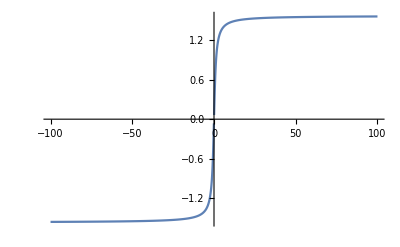

```mathematica
Plot[ArcTan[x],{x,-100,100}]
```